{{y[x]→ⅇ^x C[1]}}

{ⅇ^x C[1]}

{{y[x]→ⅇ^x}}

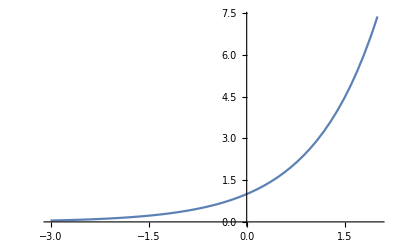

```mathematica
DSolve[{y'[x] == y[x]}, y[x], x]
y[x]/.DSolve[{y'[x] == y[x]}, y[x], x]
sol = DSolve[{y'[x] == y[x], y[0] == 1}, y[x], x]
Plot[y[x]/.sol, {x,-3,2}]
```

```mathematica
beta = 1/1000;
zeta = 95/10000;
alpha = 1/200;

(* 0 = -beta*S*Z implies either S or Z = 0.*)
(*Case 1. S = 0*)

eqns1 = {S == 0, 
		beta*S*Z + zeta*R - alpha*S*Z == 0,
		alpha*S*Z - zeta*R == 0}

Solve[eqns1, {S, Z, R}]


(*Case 2. Z = 0*)
eqns2 = {Z == 0,
		beta*S*Z + zeta*R - alpha*S*Z == 0,
		alpha*S*Z - zeta*R == 0}
		
Solve[eqns2, {S, Z, R}]
```

{S==0,(19 R)/2000-(S Z)/250==0,-(19 R)/2000+(S Z)/200==0}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{S→0,R→0}}

{Z==0,(19 R)/2000-(S Z)/250==0,-(19 R)/2000+(S Z)/200==0}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Z→0,R→0}}

```mathematica
(*SIZR Model*)
eqnsS = {0 == P - beta2*S*Z - delta2*S, 
  0 == -delta2*Q - Q*rho + beta2*S*Z, 
  0 == Q*rho - alpha2*S*Z + R*zeta2, 
  0 == delta2*Q + delta2*S + alpha2*S*Z - R*zeta2};

Solve[eqnsS, {S, Q, Z, R}];
```

```mathematica
sol = Solve[{n == s + p + r,u*n - (b/n)*p*s - v*s == 0, (b/n)*p*s - g*p - v*p == 0,g*p - v*r == 0}
, {s, p, r } ,MaxExtraConditions ->   Automatic ]
```

{{s→ConditionalExpression[0, n==0],p→ConditionalExpression[0, n==0],r→ConditionalExpression[0, n==0]},{s→ConditionalExpression[n, u==v],p→ConditionalExpression[0, u==v],r→ConditionalExpression[0, u==v]}}

```mathematica
Solve[S + Z + R == 0, -b S Z == 0 && b S Z + z R - a S Z == 0 && a S Z - z R == 0, {S, Z, R}, MaxExtraConditions->Automatic]
```

Solve::ivar: R z==0&&-R z==0 is not a valid variable.

Solve[R+Z==0,R z==0&&-R z==0,{0,Z,R},MaxExtraConditions→Automatic]